```mathematica
beta=1;    (*Initial perception rate*)
alpha=0.4; (*Critical perception rate*)
opportunisticSellerRate=0.02;
n=1000;    (*Number of steps to simulate*)
transitionMatrix[beta_,alpha_]:={{beta-alpha,1-(beta-alpha)},{beta-alpha,1-(beta-alpha)}};
markovProcess[beta_]:=DiscreteMarkovProcess[1,transitionMatrix[beta,alpha]];
transitionMatrix[beta_,alpha_]:={{beta-alpha,1-(beta-alpha)},{beta-alpha,1-(beta-alpha)}};
markovProcess[beta_]:=DiscreteMarkovProcess[1,transitionMatrix[beta,alpha]];
simulationResults=Table[If[RandomReal[]<opportunisticSellerRate,beta=Max[beta-0.1,alpha]];
process=markovProcess[beta];
RandomFunction[process,{0,1}],{n}];
initialProperties=MarkovProcessProperties[markovProcess[1]]
finalProperties=MarkovProcessProperties[markovProcess[beta]]
```

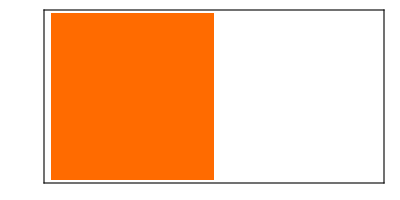
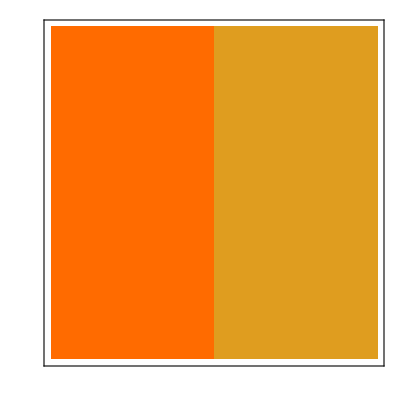
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {1.5,0.666667}
HoldingTimeVariance | {3.75,1.11111}
Structural Properties | 
CommunicatingClasses | {1,2}
RecurrentClasses | {1,2}
TransientClasses | None
AbsorbingClasses | None
PeriodicClasses | None
Periods | {}
Irreducible | True
Primitive | True
Aperiodic | True
Limiting Properties | 
LimitTransitionMatrix | -Graphics-
Reversible | True

```mathematica
Insert[initialProperties,{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

```mathematica
Insert[initialProperties,{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

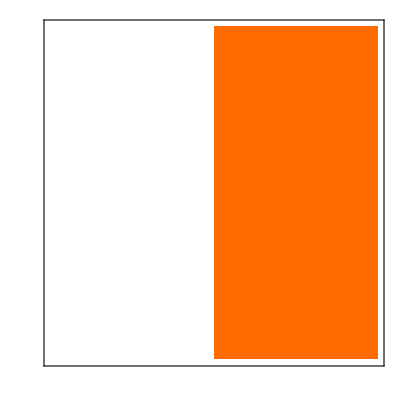
Basic Properties | 
InitialProbabilities | -Graphics-
TransitionMatrix | -Graphics-
HoldingTimeMean | {0.,∞}
HoldingTimeVariance | {0.,∞}
Structural Properties | 
CommunicatingClasses | {2}, {1}
RecurrentClasses | {2}
TransientClasses | {1}
AbsorbingClasses | {2}
PeriodicClasses | None
Periods | {∞}
Irreducible | False
Primitive | False
Aperiodic | True
Transient Properties | 
TransientVisitMean | {1.}
TransientVisitVariance | {0.}
TransientTotalVisitMean | 1.
Limiting Properties | 
ReachabilityProbability | {0.,1.}
LimitTransitionMatrix | -Graphics-
Reversible | False

```mathematica
Insert[finalProperties,{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

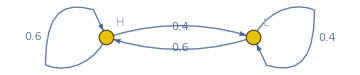

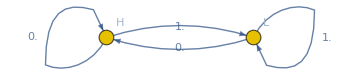

```mathematica
Graph[markovProcess[1[]],VertexLabels->{1->"H",2->"L"},VertexSize->Small,EdgeLabels->With[{sm=MarkovProcessProperties[markovProcess[1],"TransitionMatrix"]},Flatten@Table[DirectedEdge[i,j]->sm[[i,j]],{i,2},{j,2}]],ImageSize->Medium]
Graph[markovProcess[0.4[]],VertexLabels->{1->"H",2->"L"},VertexSize->Small,EdgeLabels->With[{sm=MarkovProcessProperties[markovProcess[0.4],"TransitionMatrix"]},Flatten@Table[DirectedEdge[i,j]->sm[[i,j]],{i,2},{j,2}]],ImageSize->Medium]
```

```mathematica
(*Parameters*)a=0.4;
timeSteps=1000;  (*Number of steps for the simulation*)
betaStart=1;  (*Initial β value*)
opportunisticRate=0.02;  (*2% of sellers are opportunistic*)
movingAverageWindow=100; (*Window size for the moving average, 10 to 25% of the timeSteps*)

(*Function to simulate market behavior and calculate frequency of H with moving average*)
simulateMarketBehavior[betaInitial_]:=Module[{beta,t,transitionMatrix,state,statesHistory,stateNumeric},beta=betaInitial;
state="H";
statesHistory={state};
For[t=1,t<=timeSteps,t++,If[RandomReal[]<opportunisticRate,beta=Max[beta-0.1,a];  (*Decrease beta upon encountering an opportunistic seller*)];
transitionMatrix={{beta-a,1-(beta-a)},{beta-a,1-(beta-a)}};
stateProbabilities=If[state=="H",transitionMatrix[[1]],transitionMatrix[[2]]];
state=If[RandomReal[]<stateProbabilities[[1]],"H","L"];
AppendTo[statesHistory,state];];
stateNumeric=Map[If[#=="H",1,0]&,statesHistory];
MovingAverage[stateNumeric,movingAverageWindow]];

(*Run simulations and plot results together*)
simulationResults=Table[simulateMarketBehavior[betaStart],{50}];
frequencyHPlots=ListLinePlot[simulationResults,PlotRange->{0,1},PlotLabels->"Simulations, as β starts at 1",Frame->True,FrameLabel->{"Time Step","Frequency of H"},PlotLegends->Automatic];

(*Display the plots*)
frequencyHPlots;
initialExpectation=betaStart-a;
initialExpPlot=ListLinePlot[initialExpectation,PlotRange->{0,1},PlotLabels->"Simulations, as β starts at 1",Frame->True,FrameLabel->{"Time Step","Frequency of H"},PlotLegends->Automatic];
Show[frequencyHPlots,Plot[initialExpectation,{timeSteps,1,914},PlotStyle->{Black,Thickness[0.015]},PlotLabels->"Initial Expectation"]]
```

ListLinePlot::lpn: 0.6 is not a list of numbers or pairs of numbers.

-Graphics-